```mathematica
∫_0^∞ r^4/a^2 ⅇ^(-r/a)ⅆr
```

ConditionalExpression[24 a^3, Re[a]>0]

```mathematica
∫_0^(2π) Sin[θ]^3 ⅆθ
```

0

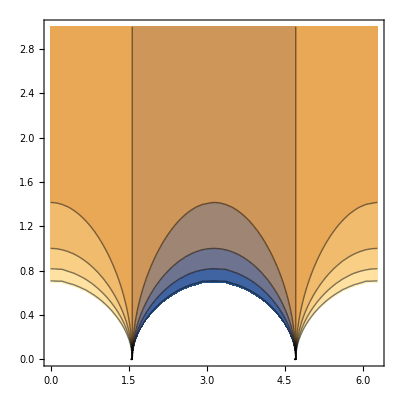

```mathematica
ContourPlot[Cos[t]/r^2,{t,0,2π},{r,0,3}]
```

```mathematica
V0= 1
```

1

```mathematica
R=5
```

5

```mathematica
P=1
```

1

```mathematica
e0=8.854×10^-12
```

8.854×10^-12

```mathematica
Solve[(V0/R-P/(4×π×e0×R^3))r×Cos[θ]+1/(4×π×e0)×(P×Cos[θ])/r^2==g,r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→5.46208×10^-14 (-679. g Sec[θ]-(580875. g^2 Sec[θ])/((6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3))-0.793701 (6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3) Sec[θ])},{r→-3.70875×10^-11 g Sec[θ]+((1.58639×10^-8+2.74772×10^-8 ⅈ) g^2 Sec[θ])/((6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3))+(2.16763×10^-14-3.75444×10^-14 ⅈ) (6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3) Sec[θ]},{r→-3.70875×10^-11 g Sec[θ]+((1.58639×10^-8-2.74772×10^-8 ⅈ) g^2 Sec[θ])/((6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3))+(2.16763×10^-14+3.75444×10^-14 ⅈ) (6.26094×10^8 g^3-6.13656×10^39 Cos[θ]^3+√(-7.68412×10^48 g^3 Cos[θ]^3+3.76574×10^79 Cos[θ]^6))^(1/3) Sec[θ]}}

```mathematica
r[g_,θ_]:=((√Cos[θ])/(√g))
```

```mathematica
cValues={0.00001,0.01,0.05,0.1,0.3,0.6,1.0,1.5,2.0,2.5,3.2}
```

{0.00001,0.01,0.05,0.1,0.3,0.6,1.,1.5,2.,2.5,3.2}

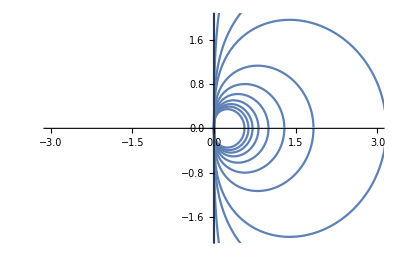

```mathematica
PolarPlot[r[#,θ],{θ,0.01,2 π},AspectRatio->Automatic,PlotRange->{{-3,3},{-2,2}},PlotPoints->1000]&/@cValues//Show
```

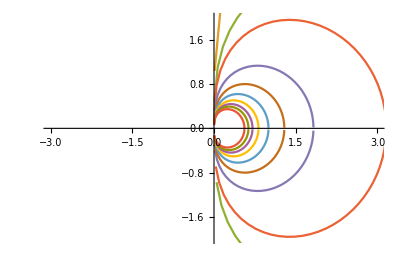

```mathematica
ListPolarPlot[Table[{θ,r[#,θ]},{θ,0.01,2 π,0.05}]&/@cValues//Chop,AspectRatio->Automatic,PlotRange->{{-3,3},{-2,2}},Joined->True]
```

```mathematica
With[{a=1},implicitPlot[(r^2-a^3/r) Sin[theta]^2==#1,{r,0,3},{theta,0,2 π},"Polar",PlotPoints->51,AspectRatio->Automatic]&/@cValues//Show]
```

Show::gcomb: Could not combine the graphics objects in Show[{implicitPlot[(-Power[«2»] + SuperscriptBox[r, 2])\\\ SuperscriptBox[Sin[theta], 2] == 0.00001, {r, 0, 3}, {theta, 0, 2\\\ π}, \"\<Polar\>\", PlotPoints → 51, AspectRatio → Automatic], implicitPlot[(-Power[«2»] + SuperscriptBox[r, 2])\\\ SuperscriptBox[Sin[theta], 2] == 0.01, {r, 0, 3}, {theta, 0, 2\\\ π}, \"\<Polar\>\", PlotPoints → 51, AspectRatio → Automatic], «7», implicitPlot[(-Power[«2»] + SuperscriptBox[r, 2])\\\ SuperscriptBox[Sin[theta], 2] == 2.5, {r, 0, 3}, {theta, 0, 2\\\ π}, \"\<Polar\>\", PlotPoints → 51, AspectRatio → Automatic], «1»}].

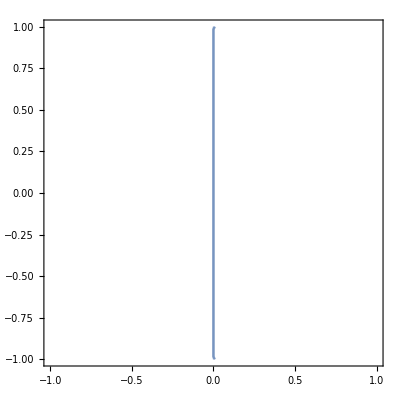

```mathematica
cValues={1,2,3,4,5};
Block[{R=1},ParametricPlot[r {Cos[θ],Sin[θ]},{r,0,R},{θ,0,2 Pi},PlotStyle->None,BoundaryStyle->None,PlotPoints->{60,120},MeshFunctions->{Function[{x,y,r,θ},(V0/R-P/(4×π×e0×R^3))r×Cos[θ]+1/(4×π×e0)×(P×Cos[θ])/r^2]},Mesh->{cValues},MeshStyle->{Directive[ColorData[97][1],AbsoluteThickness[1.6]]},Method->{"BoundaryOffset"->True}]]
```